#### Data thief existing constraints of Q vs. m_s (lines on log-log scale)

```mathematica
OA1={{1.9882697947214076,34.76014760147601},
{2.8592375366568916,33.726937269372684}};
OA2={{2.8592375366568916,33.726937269372684},{
2.348973607038123,31.586715867158667}};
TA1={{2.348973607038123,31.586715867158667},{
3.736070381231672,29.815498154981544}};
TA2={{3.736070381231672,29.815498154981544},{
1.9882697947214076,22.50922509225092}};
SuperK={{1.9912023460410557,25.461254612546117},{
4.69208211143695,21.992619926199257}};
Stability={{1.9882697947214076,10.84870848708487},{
5.011730205278592,23.025830258302577}};
```

```mathematica
OA1plot=Plot[Interpolation[OA1,InterpolationOrder->1][x],{x,1,2.8592375366568916},PlotStyle->{Red}];
OA2plot=Plot[Interpolation[OA2,InterpolationOrder->1][x],{x,2.348973607038123,2.8592375366568916},PlotStyle->{Red}];
TA1plot=Plot[Interpolation[TA1,InterpolationOrder->1][x],{x,2.348973607038123,3.736070381231672},PlotStyle->{Red}];
TA2plot=Plot[Interpolation[TA2,InterpolationOrder->1][x],{x,2.5,3.736070381231672},PlotStyle->{Red}];
SuperKplot=Plot[Interpolation[SuperK,InterpolationOrder->1][x],{x,2.5,4.8},PlotStyle->{Red}];
Stabilityplot=Plot[Interpolation[Stability,InterpolationOrder->1][x],{x,1,8},PlotStyle->{Red,Dashed}];
```

InterpolatingFunction::dmval: Input value {1.00004} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.00014} lies outside the range of data in the interpolating function. Extrapolation will be used.

#### Our limits

```mathematica
Qballboom[x_]:=41.80158027195581+ 4(x-3)
QballNuStar[x_]:=59.54572245905269-4/3(x-3)
QballRX[x_]:=55.01513578082331-4/3(x-3)
Qballgravity[x_]:=53.7347066608853-4/3(x-3)
Qballtrigger[x_]:=49.20411998265592+ 4(x-3)
QballBH[x_]:=64-4(x-3)
boom=Plot[Qballboom[x],{x,1,8},PlotStyle->{Purple}];
friction=Plot[Qballgravity[x],{x,1,8},PlotStyle->{Brown}];
trigger=Plot[Qballtrigger[x],{x,1,8},PlotStyle->{Black}];
NuStar=Plot[QballNuStar[x],{x,1,8},PlotStyle->{Gray}];
RX=Plot[QballRX[x],{x,1,8},PlotStyle->{Blue}];
BH=Plot[QballBH[x],{x,1,8},PlotStyle->{Orange}];
excludedRX=RegionPlot[{y≥Qballboom[x]&& y≤Min[QballRX[x],QballBH[x]]},{x,1,8},{y,10,70}];
excludedBH=RegionPlot[{y≥QballBH[x]},{x,1,10},{y,10,70},PlotStyle->{LightOrange},PlotPoints->100];
excludedNuStar=RegionPlot[{y≥Qballboom[x]&& y≤Min[QballNuStar[x],QballBH[x]]},{x,1,10},{y,10,70},PlotPoints->100];
excludedNuStarGravity=RegionPlot[{y≥Qballgravity[x]&& y≤Min[QballNuStar[x],QballBH[x],Qballtrigger[x]]},{x,1,10},{y,10,70},PlotPoints->100];
XLabelQ={{2,"10^2"},{3,"10^3"},{4,"10^4"},{5,"10^5"},{6,"10^6"},{7,"10^7"}};
YLabelQ={{20,"10^20"},{30,"10^30"},{40,"10^40"},{50,"10^50"},{60,"10^60"},{70,"10^70"}};
canvasQball=Plot[-1,{x,2,6.7},PlotRange->{21,65},Frame->True,FrameTicks->{{YLabelQ,None},{XLabelQ,None}},FrameStyle->Black,FrameLabel->{"m_S (GeV)","Q"},LabelStyle-> Directive[Bold]];
```

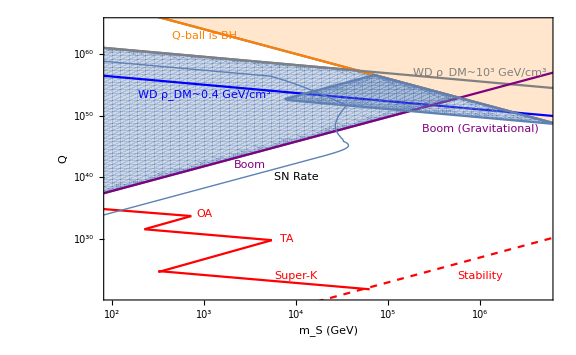

```mathematica
Show[canvasQball,OA1plot,OA2plot,TA1plot,TA2plot,SuperKplot,Stabilityplot,excludedBH,excludedNuStar,BH,NuStar,RX,boom,normalSN,endSN,excludedNuStarGravity,Graphics[Inset[Style["OA",Small,Red,FontFamily->"Helvetica"],{3,34},{0,0},1,{1,0}]],Graphics[Inset[Style["TA",Small,Red,FontFamily->"Helvetica"],{3.9,30},{0,0},1,{1,0}]],Graphics[Inset[Style["Super-K",Small,Red,FontFamily->"Helvetica"],{4,24},{0,0},1,{1,0}]],Graphics[Inset[Style["Stability",Small,Red,FontFamily->"Helvetica"],{6,24},{0,0},2,{1,1/5}]],Graphics[Inset[Style["Boom",Small,Purple,FontFamily->"Helvetica"],{3.5,42},{0,0},2,{1,1/4}]],Graphics[Inset[Style["Q-ball is BH",Small,Orange,FontFamily->"Helvetica"],{3,63},{0,0},2,{1,-1/4}]],Graphics[Inset[Style["WD ρ_DM~0.4 GeV/cm^3",Small,Blue,FontFamily->"Helvetica"],{3,53.5},{0,0},2,{1,-1/12.5}]],Graphics[Inset[Style["WD ρ_DM~10^3 GeV/cm^3",Small,Gray,FontFamily->"Helvetica"],{6,57},{0,0},2,{1,-1/12.5}]],
Graphics[Inset[Style["SN Rate",Small,FontFamily->"Helvetica"],{4,40},{0,0},2,{1,1/4}]],
Graphics[Inset[Style["Boom (Gravitational)",Small,Purple,FontFamily->"Helvetica"],{6,48},{0,0},2,{1,-1/12.5}]],

ImageSize->Large]
```

#### dynamical friction (m_s in GeV)

```mathematica
Solve[10^4/((10^19 GeV)^2)(10^ms GeV)Q^(3/4)==(4 10^-5 cm)/(0.2 GeV*10^-13 cm),Q]
```

{{Q→5.42884×10^57 (10.^-ms)^(4/3)}}

```mathematica
Log10[5.428835233189812*^57 (10.^-ms)^(4/3)]/.ms->3
```

53.7347

```mathematica
Log10[(10^ms GeV(4 10^-5 cm)1/(0.2 GeV *10^-13 cm))^4]/.ms->3
```

49.2041